```mathematica
ChromaticPolynomial[ReadGraph[8,12],3]
```

6

```mathematica
TableForm[Table[With[{g=ReadGraph[8,k]},{k,DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]],Graph[g,GraphHighlight->EdgesWith[g,7],GraphHighlightStyle->"Dashed",VertexLabels->"Name",GraphHighlightStyle->"Dashed",VertexLabels->"Name", GraphLayout->"PlanarEmbedding", ImageSize->Tiny]}],{k,1,14}]]
```

1 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
2 | x→0.+0. ⅈ
x→1.
x→2.
x→2.5466
x→3.
x→3.2267+1.46771 ⅈ
x→3.2267-1.46771 ⅈ | -Graphics-
3 | x→0.+0. ⅈ
x→1.
x→2.
x→2.67781
x→3.
x→3.16109+1.75438 ⅈ
x→3.16109-1.75438 ⅈ | -Graphics-
4 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
5 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
6 | x→0.+0. ⅈ
x→1.
x→2.
x→2.5466
x→3.
x→3.2267+1.46771 ⅈ
x→3.2267-1.46771 ⅈ | -Graphics-
7 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
8 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
9 | x→0.+0. ⅈ
x→1.
x→2.
x→2.61497
x→2.88928-2.06647 ⅈ
x→2.88928+2.06647 ⅈ
x→3.
x→3.60646 | -Graphics-
10 | x→0.+0. ⅈ
x→1.
x→2.
x→2.5466
x→3.
x→3.2267+1.46771 ⅈ
x→3.2267-1.46771 ⅈ | -Graphics-
11 | x→0.+0. ⅈ
x→1.
x→2.
x→2.5466
x→3.
x→3.2267+1.46771 ⅈ
x→3.2267-1.46771 ⅈ | -Graphics-
12 | x→0.+0. ⅈ
x→1.
x→2.
x→2.59483
x→2.76469-0.754442 ⅈ
x→2.76469+0.754442 ⅈ
x→3.43789-1.93908 ⅈ
x→3.43789+1.93908 ⅈ | -Graphics-
13 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-
14 | x→0.+0. ⅈ
x→1.
x→2.
x→2.99375
x→2.99695
x→2.99953
x→3.00427
x→3.00446 | -Graphics-

```mathematica
-332+498 x-303 x^2+94 x^3-15 x^4+x^5
```

-332+498 x-303 x^2+94 x^3-15 x^4+x^5

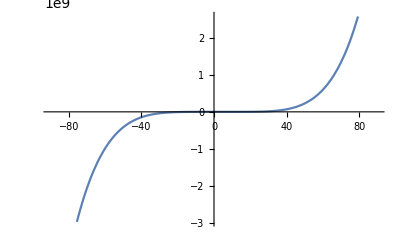

```mathematica
Plot[-332+498 x-303 x^2+94 x^3-15 x^4+x^5,{x,-90.,90.}]
```

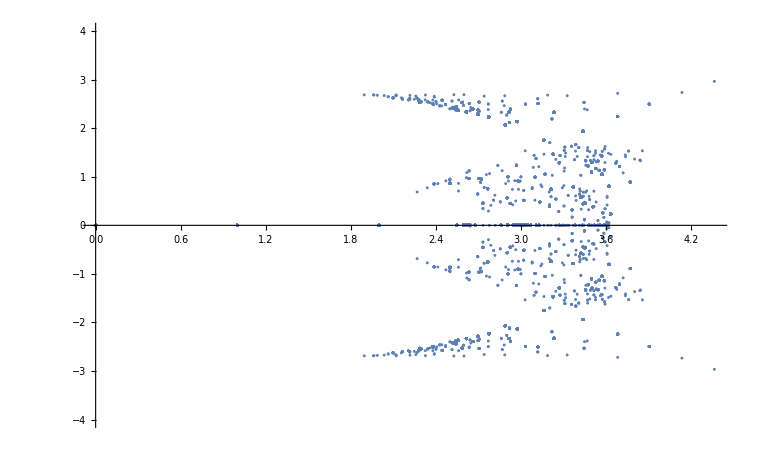

```mathematica
Monitor[
ListPlot[
Map[{Re[#],Im[#]}&,
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[12,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,7594}]],1]
],
PlotRange->{Automatic,{-4,4}}
],k]
```

```mathematica
Monitor[
ListPlot[
Map[{Re[#],Im[#]}&,
Join[
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[5,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,1}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[6,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,2}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[7,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,5}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[8,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,14}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[9,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,50}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[10,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,233}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[11,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,1249}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[12,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,7594}]],1],
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[13,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,30000}]],1]
]
],
PlotRange->All
],k]
```

-Graphics-

```mathematica
Show[%,PlotRange->{{2,4},All}]
```

-Graphics-

```mathematica
Flatten[Map[x/.#&,Table[With[{g=ReadGraph[8,k]},DeleteDuplicates[NSolve[ChromaticPolynomial[g,x]==0,x]]],{k,1,14}]],1]
```

{0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.5466,3.,3.2267+1.46771 ⅈ,3.2267-1.46771 ⅈ,0.+0. ⅈ,1.,2.,2.67781,3.,3.16109+1.75438 ⅈ,3.16109-1.75438 ⅈ,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.5466,3.,3.2267+1.46771 ⅈ,3.2267-1.46771 ⅈ,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.61497,2.88928-2.06647 ⅈ,2.88928+2.06647 ⅈ,3.,3.60646,0.+0. ⅈ,1.,2.,2.5466,3.,3.2267+1.46771 ⅈ,3.2267-1.46771 ⅈ,0.+0. ⅈ,1.,2.,2.5466,3.,3.2267+1.46771 ⅈ,3.2267-1.46771 ⅈ,0.+0. ⅈ,1.,2.,2.59483,2.76469-0.754442 ⅈ,2.76469+0.754442 ⅈ,3.43789-1.93908 ⅈ,3.43789+1.93908 ⅈ,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446,0.+0. ⅈ,1.,2.,2.99375,2.99695,2.99953,3.00427,3.00446}